# Wilberforce Pendulum modelling PHYS1201 ASE project, 2022

## By Campbell McTernan and Aditya Singh Tejas

## Introduction

This project requires the creation and investigation of a complex mechanical system as least as complex as a double pendulum. For this task, we have chosen the Wilberforce pendulum which was first described by the physicist Lionel Robert Wilberforce  in 1896. The Wilberforce pendulum is constructed by hanging  a mass which is free to rotate in the direction of the coils, with certain harmonic properties which allow for energy to alternate between purely vertical and rotational motion. This is achieved through a coupling of the rotational and spring potential energy of the system. To extend this concept we have placed the system on a free support and allowed for a sideways swinging motion. To our knowledge, this setup has never been modeled before.

This project focuses on the description and analysis of the pendulum, using the Euler-Lagrange equations of motion to predict the pendulum’s path and subsequently compare numerical simulations of the system with experimental data. This document primarily serves to describe the theoretical implications of design choices for the pendulum and to predict its path using computational software.

## The Wilberforce Pendulum With Free Support

The mass  is free to slide along a frictionless rail. The Wilberforce pendulum consists of a cylindrical mass  (length  and moment of inertia ) suspended at its mid-point by a helical spring of natural length , stretched length l + s(t), longitudinal spring constant  and torsional spring constant . We assume that the spring has negligible mass and is rigid along its axis throughout the experiment. The cylinder must hang such that its axis is always in the plane orthogonal to the direction of the spring, and is able to rotate along this plane. The spring makes an angle  from the vertical and the tracked point on the cylinder creates an angle  measured from its starting point in the rotational plane: see Figure 2 . The horizontal position of the mass  is noted as  from the origin  : see Figure 1. We choose the reference of the gravitational potential energy to be zero at the height of the origin. Note that the motion is actually in 3 dimensions but the direction into the page is essentially irrelevant to our defined equations of motion, as it can be represented by .


	-Graphics-


Note that there are four coordinates, that is, θ, ,  and . Thus there will be four Euler-Lagrange equations which must be solved simultaneously.

## Deriving the Euler-Lagrange equations

We start by deriving the kinetic and potential energies, and hence the Lagrangian. 

Kinetic energy

As the entire system is free to slide along a rail, the whole system can obtain a common velocity and thus kinetic energy. Defining  to be the velocity of the system in the  direction, we have  . Furthermore, the cylinder will have velocity relative to the system  and rotational energy dependant on the rotational velocity  given by  and  . 

Hence, the total kinetic energy of the system is , so

Potential energy

We know that a spring with spring constant  and stretch length  has a spring potential  . We also know that the torsional potential of the spring is . Since these potentials are coupled, we furthermore have the potential  which represents the shared energy held during the transfer of energy between  and  in the system. As there are only two coupled components of potential, this relationship is linear and proportional to  and . Thus, assume  where  is some constant. Finally, as this Wilberforce experiment has been made unique by the inclusion of traditional swinging pendulum motion, we also have gravitational potential  . 

Thus, the total kinetic energy of the system is  , so

Lagrangian

The Lagrangian is given by , so evaluating with our previous answers and simplifying gives:

### Computational Solutions for the Lagrangian

When defining the quantities for potential and kinetic energy mathematically, it is most convenient to use Cartesian coordinates:

```mathematica
Subscript[x, 0] = x[t]; Subscript[y, 0] = 0;
Subscript[x, 1]=(Subscript[L, spring]+ Subscript[L, connect] + Subscript[L, tube]+ s[t]) Sin[ θ[t]]+ Subscript[x, 0];Subscript[y, 1]=-(Subscript[L, spring]+ Subscript[L, connect] + Subscript[L, tube]+ s[t]) Cos[θ[t]]+Subscript[y, 0];
Subscript[x, 2]=(0.5*Subscript[L, bolt])Cos[α[t]] Cos[ θ[t]]+Subscript[x, 1] + (0.5*Subscript[L, cylinder]  + Subscript[L, glue]- Subscript[r, bolt])Sin[θ[t]];Subscript[y, 2]=(0.5*Subscript[L, bolt])Cos[α[t]] Sin[ θ[t]]+Subscript[y, 1]- (0.5*Subscript[L, cylinder]  + Subscript[L, glue]- Subscript[r, bolt])Cos[θ[t]];
i = Subscript[m, cylinder] * Subscript[r, cylinder]^2 + 1/12 * Subscript[m, bolt] * Subscript[L, bolt]^2;
```

Where ,  and  respectively represents the coordinates of the mass , the cylinder , and the tracking point from the origin. Also note that  is the formula for the moment of inertia  of the cylinder.

Using The kinetic energy is then:

```mathematica
ke=0.5 (Subscript[m, free]+Subscript[M, bob]) (D[Subscript[x, 0],t]^2)+0.5 Subscript[M, bob](D[Subscript[x, 1],t]^2+D[Subscript[y, 1],t]^2)+0.5 i ((D[α[t], t])^2)
```

0.2675 x'[t]^2+0.000417221 α'[t]^2+0.2575 ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t])^2+(-Cos[θ[t]] s'[t]-(-0.1358-s[t]) Sin[θ[t]] θ'[t])^2)

Which simplifies to:

```mathematica
ke=FullSimplify[ke]
```

0.2675 x'[t]^2+0.000417221 α'[t]^2+0.2575 ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t])^2+(Cos[θ[t]] s'[t]-1. (0.1358+s[t]) Sin[θ[t]] θ'[t])^2)

Choose the gravitational potential energy zero to be at y_1 = 0 :

```mathematica
ve=0.5 k *s[t]^2 + 0.5 δ α [t]^2  +  ϕ α[t] s[t]- Subscript[M, bob]*g Cos [θ[t]](Subscript[L, spring]+ s[t] )
```

0.5 k s[t]^2-0.515 g Cos[θ[t]] (0.076+s[t])+ϕ s[t] α[t]+0.5 δ α[t]^2

So the potential energy simplifies to:

```mathematica
ve=FullSimplify[ve]
```

0.5 k s[t]^2-0.515 g Cos[θ[t]] (0.076+s[t])+ϕ s[t] α[t]+0.5 δ α[t]^2

The Lagrangian is then calculated:

```mathematica
lgr=ke-ve
```

-0.5 k s[t]^2+0.515 g Cos[θ[t]] (0.076+s[t])-ϕ s[t] α[t]-0.5 δ α[t]^2+0.2675 x'[t]^2+0.000417221 α'[t]^2+0.2575 ((Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t])^2+(Cos[θ[t]] s'[t]-1. (0.1358+s[t]) Sin[θ[t]] θ'[t])^2)

We next calculate all partial derivatives needed in the Euler-Lagrange equation:

```mathematica
dLdθ=D[lgr,θ[t]] (* θ derivative *)
```

-0.515 g (0.076+s[t]) Sin[θ[t]]+0.2575 (2 (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t]) (Cos[θ[t]] s'[t]-(0.1358+s[t]) Sin[θ[t]] θ'[t])+2 (-Sin[θ[t]] s'[t]-1. Cos[θ[t]] (0.1358+s[t]) θ'[t]) (Cos[θ[t]] s'[t]-1. (0.1358+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdα=D[lgr,α[t]] (* α derivative *)
```

-ϕ s[t]-1. δ α[t]

```mathematica
dLds=D[lgr,s[t]] (* s derivative *)
```

0.515 g Cos[θ[t]]-1. k s[t]-ϕ α[t]+0.2575 (2 Cos[θ[t]] θ'[t] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t])-2. Sin[θ[t]] θ'[t] (Cos[θ[t]] s'[t]-1. (0.1358+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
5.0449399999999995 Cos[θ[t]]-47.8 s[t]-0.003 α[t]+0.2575 (2 Cos[θ[t]] θ'[t] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1739+s[t]) θ'[t])-2. Sin[θ[t]] θ'[t] (Cos[θ[t]] s'[t]-1. (0.1739+s[t]) Sin[θ[t]] θ'[t]))
```

5.04494 Cos[θ[t]]-47.8 s[t]-0.003 α[t]+0.2575 (2 Cos[θ[t]] θ'[t] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1739+s[t]) θ'[t])-2. Sin[θ[t]] θ'[t] (Cos[θ[t]] s'[t]-1. (0.1739+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdx=D[lgr,x[t]] (* x derivative *)
```

0

```mathematica
dLdashdx=D[lgr,x'[t]] (* x' derivative *)
```

0.535 x'[t]+0.515 (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t])

```mathematica
dLdashds=D[lgr,s'[t]] (* s' derivative *)
```

0.2575 (2 Sin[θ[t]] (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t])+2 Cos[θ[t]] (Cos[θ[t]] s'[t]-1. (0.1358+s[t]) Sin[θ[t]] θ'[t]))

```mathematica
dLdashdα=D[lgr,α'[t]] (* α' derivative *)
```

0.000834442 α'[t]

```mathematica
dLdashdθ=D[lgr,θ'[t]] (* θ' derivative *)
```

0.2575 (2 Cos[θ[t]] (0.1358+s[t]) (Sin[θ[t]] s'[t]+x'[t]+Cos[θ[t]] (0.1358+s[t]) θ'[t])-2. (0.1358+s[t]) Sin[θ[t]] (Cos[θ[t]] s'[t]-1. (0.1358+s[t]) Sin[θ[t]] θ'[t]))

We then calculate the Euler-Lagrange equations for θ,  α,  and :

```mathematica
ELEθ=0==FullSimplify[dLdθ-D[dLdashdθ,t]]
```

0==-0.03914 g Sin[θ[t]]-0.139874 s'[t] θ'[t]-0.069937 Cos[θ[t]] x''[t]-0.00949744 θ''[t]+s[t] (-0.515 g Sin[θ[t]]-1.03 s'[t] θ'[t]-0.515 Cos[θ[t]] x''[t]+(-0.139874-0.515 s[t]) θ''[t])

```mathematica
ELEα= 0==FullSimplify[dLdα-D[dLdashdα,t]]
```

0==-ϕ s[t]-1. δ α[t]-0.000834442 α''[t]

```mathematica
ELEs= 0==FullSimplify[dLds-D[dLdashds,t]]
```

0==0.515 g Cos[θ[t]]-1. ϕ α[t]+0.069937 θ'[t]^2+s[t] (-1. k+0.515 θ'[t]^2)-0.515 s''[t]-0.515 Sin[θ[t]] x''[t]

```mathematica
ELEx= 0==FullSimplify[dLdx-D[dLdashdx,t]]
```

0==-1.03 Cos[θ[t]] s'[t] θ'[t]+0.515 (0.1358+s[t]) Sin[θ[t]] θ'[t]^2-0.515 Sin[θ[t]] s''[t]-1.05 x''[t]-0.515 Cos[θ[t]] (0.1358+s[t]) θ''[t]

## Numerically solving the Euler-Lagrange equations

The initial parameters are now chosen (see reference for more information).

```mathematica
Subscript[L, free] = 0.015; Subscript[L, spring] = 0.076; k = 47.8; δ = 0.00089; Subscript[L, connect] = 0.0358; Subscript[L, cylinder]= 0.1242; Subscript[M, bob] = 0.515; Subscript[L, bolt] = 0.1228; Subscript[L, nut] = 0.0127; Subscript[m, bolt]= 0.056; Subscript[r, cylinder]= 0.0408;Subscript[m, cylinder] = 0.459; g = 9.796;  ϕ = 0.003; Subscript[r, bolt] = 0.00635; Subscript[L, glue] = 0.0154; Subscript[L, tube] = 0.024;
```

#### Situation 1: Traditional Wilberforce Pendulum

In this example we will approximate the Wilberforce pendulum without a free support or swinging motion. This is achieved by initialising the pendulum on the vertical with a free support mass orders of magnitude larger than the cylinder.

```mathematica
Subscript[m, free]=4000;
```

Initialising and solving the Euler-Lagrange equations (we are setting the cylinder to be at rest vertically but with significant spinning):

```mathematica
solndp1=NDSolve[{ELEθ,ELEα,ELEs,ELEx,θ[0]==0,α[0]==3*Pi/2,θ'[0]==0,α'[0]== 0, s[0] == 0.05, s'[0] == 0, x[0] == 0.365, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plotting y_1 and y_2 coordinates vs time. Note that y_1 is the heights of the centre of the cylinder, while y_2 is the point on the edge: thus they will be quite close .

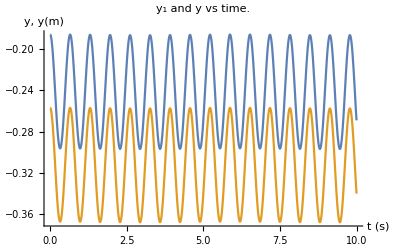

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp1],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y(m)"},PlotLabel->"y_1 and y vs time."]
```

Plotting the free support, cylinder and tracking point trajectories in x, y plane.

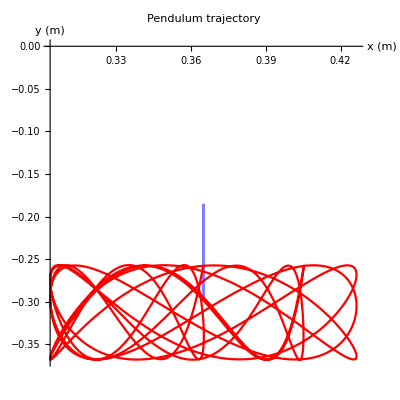

```mathematica
ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp1,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle->{Green, {Opacity[0.5],Blue}, Red}],AspectRatio->1, PlotRange-> {-1,1}]
```

Animation of trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp1,{t,0,tend},PlotRange->{{0.25,0.46},{-0.19,-0.35}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle->{Green, {Opacity[0.5],Blue}, Red}],AspectRatio->1],{tend,0,10},AnimationRepetitions->3,AnimationRate->0.75]
```

### Adding damping 1

To simulate energy losses due to heat/friction we will also  add terms proportional to each of the variables θ, ,  and .  with air resistance , free support resistance , and spring loss rate .

The damped dynamical equations are thus:

```mathematica
ELEθDamped1=0==FullSimplify[D[dLdashdθ,t]-dLdθ +β θ'[t]]
```

0==0.383415 Sin[θ[t]]+(1. β+0.139874 s'[t]) θ'[t]+0.069937 Cos[θ[t]] x''[t]+0.00949744 θ''[t]+s[t] (5.04494 Sin[θ[t]]+1.03 s'[t] θ'[t]+0.515 Cos[θ[t]] x''[t]+(0.139874+0.515 s[t]) θ''[t])

```mathematica
ELEαDamped1=0==FullSimplify[D[dLdashdα,t]-dLdα +β α'[t]]
```

0==0.003 s[t]+0.00089 α[t]+β α'[t]+0.000834442 α''[t]

```mathematica
ELEsDamped1=0==FullSimplify[D[dLdashds,t]-dLds +μ s'[t]]
```

0==-5.04494 Cos[θ[t]]+0.003 α[t]+1. μ s'[t]-0.069937 θ'[t]^2+s[t] (47.8-0.515 θ'[t]^2)+0.515 s''[t]+0.515 Sin[θ[t]] x''[t]

```mathematica
ELExDamped1=0==FullSimplify[D[dLdashdx,t]-dLdx +γ x'[t]]
```

0==γ x'[t]+1.03 Cos[θ[t]] s'[t] θ'[t]-0.515 (0.1358+s[t]) Sin[θ[t]] θ'[t]^2+0.515 Sin[θ[t]] s''[t]+1.05 x''[t]+0.515 Cos[θ[t]] (0.1358+s[t]) θ''[t]

Choosing the damping parameter to be quite small and solving the Euler-Lagrange equation we get:

```mathematica
β=0.005; μ = 0.003; γ = 0.02; solnD1=NDSolve[{ELEθDamped1,ELEαDamped1,ELEsDamped1,ELExDamped1,θ[0]==0,α[0]==3*Pi/2,θ'[0]==0,α'[0]== 0, s[0] == 0.05, s'[0] == 0, x[0] == 0.365, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plotting y_1 and y_2 coordinates vs time. Note that y_1 is the heights of the centre of the cylinder, while y_2 is the point on the edge: thus they will be quite close .

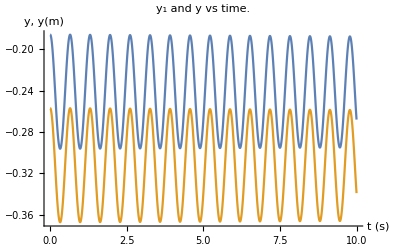

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solnD1],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y(m)"},PlotLabel->"y_1 and y vs time."]
```

Plotting the free support, cylinder and tracking point trajectories in x, y plane.

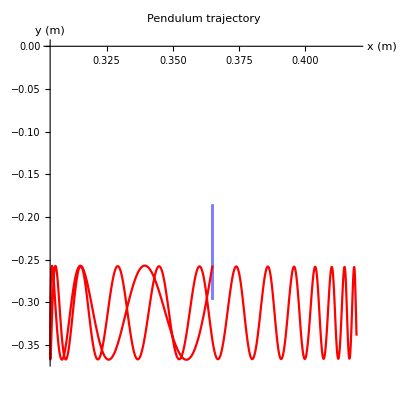

```mathematica
ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solnD1,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle -> {{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red}], AspectRatio->1]
```

Animation of trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solnD1,{t,0,tend},PlotRange->{{-0.05,0.15},{-4,0}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle -> {{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red}],AspectRatio->1],{tend,0,10},AnimationRepetitions->3,AnimationRate->0.75]
```

#### Situation 2: Wilberforce Pendulum with Swing

In this example we will approximate the Wilberforce pendulum without a free support but with a  swinging motion. This is achieved by initialising the pendulum on the horizontal with a free support mass orders of magnitude larger than the cylinder.

```mathematica
Subscript[m, free]=4000;
```

Initialising and solving the Euler-Lagrange equations (we are setting the cylinder to have gravitational potential and spin):

```mathematica
solndp2=NDSolve[{ELEθ,ELEα,ELEs,ELEx,θ[0]== 26.9*Pi/180,α[0]==Pi,θ'[0]==0,α'[0]== 0, s[0] == 0.044, s'[0] == 0, x[0] == 0.415, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plotting y_1 and y_2 coordinates vs time. Note that y_1 is the heights of the centre of the cylinder, while y_2 is the point on the edge: thus they will be quite close .

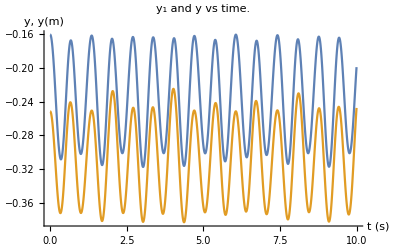

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp2],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y(m)"},PlotLabel->"y_1 and y vs time."]
```

Plotting the free support, cylinder and tracking point trajectories in x, y plane.

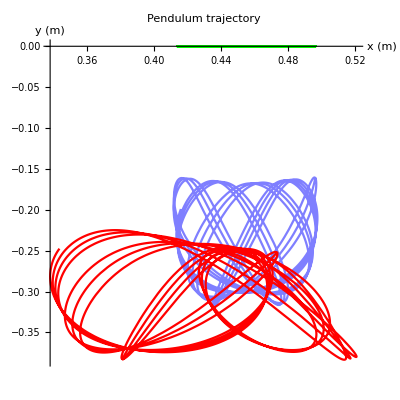

```mathematica
ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp2,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle->{Green, {Opacity[0.5],Blue}, Red}], AspectRatio->1]
```

Animation of trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp2,{t,0,tend},PlotRange->{{-0.5,0.33},{0,-0.5}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle->{Green, {Opacity[0.5],Blue}, Red}], AspectRatio->1],{tend,0,10},AnimationRepetitions->3,AnimationRate->0.75]
```

### Adding damping 2

To simulate energy losses due to heat/friction we will also  add terms proportional to each of the variables θ, ,  and .  with air resistance , free support resistance , and spring loss rate .

The damped dynamical equations are thus:

```mathematica
ELEθDamped2=0==FullSimplify[D[dLdashdθ,t]-dLdθ +β θ'[t]]
```

0==0.383415 Sin[θ[t]]+(0.005+0.139874 s'[t]) θ'[t]+0.069937 Cos[θ[t]] x''[t]+0.00949744 θ''[t]+s[t] (5.04494 Sin[θ[t]]+1.03 s'[t] θ'[t]+0.515 Cos[θ[t]] x''[t]+(0.139874+0.515 s[t]) θ''[t])

```mathematica
ELEαDamped2=0==FullSimplify[D[dLdashdα,t]-dLdα +β α'[t]]
```

0==0.003 s[t]+0.00089 α[t]+0.005 α'[t]+0.000834442 α''[t]

```mathematica
ELEsDamped2=0==FullSimplify[D[dLdashds,t]-dLds +μ s'[t]]
```

0==-5.04494 Cos[θ[t]]+0.003 α[t]+0.003 s'[t]-0.069937 θ'[t]^2+s[t] (47.8-0.515 θ'[t]^2)+0.515 s''[t]+0.515 Sin[θ[t]] x''[t]

```mathematica
ELExDamped2=0==FullSimplify[D[dLdashdx,t]-dLdx +γ x'[t]]
```

0==0.02 x'[t]+1.03 Cos[θ[t]] s'[t] θ'[t]-0.515 (0.1358+s[t]) Sin[θ[t]] θ'[t]^2+0.515 Sin[θ[t]] s''[t]+1.05 x''[t]+0.515 Cos[θ[t]] (0.1358+s[t]) θ''[t]

Choosing the damping parameter to be quite small and solving the Euler-Lagrange equation we get:

```mathematica
β=0.005; μ = 0.003; γ = 0.02; solnD2=NDSolve[{ELEθDamped2,ELEαDamped2,ELEsDamped2,ELExDamped2,θ[0]== 26.9*Pi/180,α[0]==Pi,θ'[0]==0,α'[0]== 0, s[0] == 0.044, s'[0] == 0, x[0] == 0.415, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plotting y_1 and y_2 coordinates vs time. Note that y_1 is the heights of the centre of the cylinder, while y_2 is the point on the edge: thus they will be quite close .

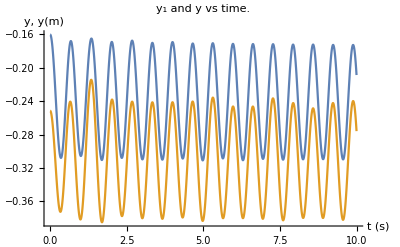

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solnD2],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y(m)"},PlotLabel->"y_1 and y vs time."]
```

Plotting the free support, cylinder and tracking point trajectories in x, y plane.

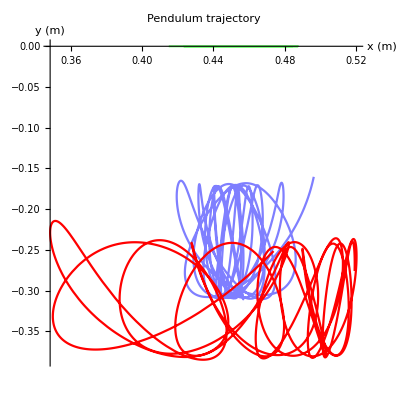

```mathematica
ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solnD2,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle -> {{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red}], AspectRatio->1]
```

Animation of trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solnD2,{t,0,tend},PlotRange->{{-0.05,0.15},{-4,0}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle -> {{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red}],AspectRatio->1],{tend,0,10},AnimationRepetitions->3,AnimationRate->0.75]
```

#### Situation 3: Wilberforce Pendulum with Swing and Free Support

In this example we will demonstrate the Wilberforce pendulum with a high degree of flexibility: having a negligible free support mass and full incentive for swinging motion.

```mathematica
Subscript[m, free] = 0.02;
```

Initialising and solving the Euler-Lagrange equations (we are setting the cylinder to have gravitational potential and spin):

```mathematica
solndp3=NDSolve[{ELEθ,ELEα,ELEs,ELEx,θ[0]== 46.7*Pi/180,α[0]==Pi,θ'[0]==0,α'[0]== 0, s[0] == 0.0126, s'[0] == 0, x[0] == 0.409, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plotting y_1 and y_2 coordinates vs time. Note that y_1 is the heights of the centre of the cylinder, while y_2 is the point on the edge: thus they will be quite close .

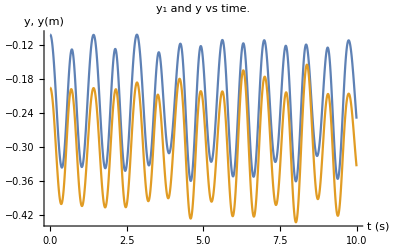

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp3],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y(m)"},PlotLabel->"y_1 and y vs time."]
```

Plotting the free support, cylinder and tracking point trajectories in x, y plane.

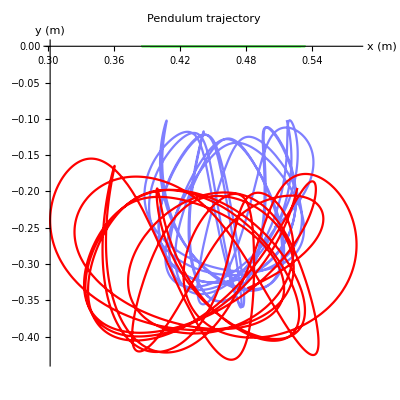

```mathematica
ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp3,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle->{{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red}], AspectRatio->1]
```

Animation of trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp3,{t,0,tend},PlotRange->{{-0.07,0.25},{0,-0.5}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle -> {{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red} ], AspectRatio->1],{tend,0,10},AnimationRepetitions->3, AnimationRate->0.75]
```

```mathematica
|
```

### Adding damping 3

To simulate energy losses due to heat/friction we will also  add terms proportional to each of the variables θ, ,  and  with the same proportionality constant .

The damped dynamical equations are thus:

```mathematica
ELEθDamped3=0==FullSimplify[D[dLdashdθ,t]-dLdθ +β θ'[t]]
```

0==0.383415 Sin[θ[t]]+(0.005+0.139874 s'[t]) θ'[t]+0.069937 Cos[θ[t]] x''[t]+0.00949744 θ''[t]+s[t] (5.04494 Sin[θ[t]]+1.03 s'[t] θ'[t]+0.515 Cos[θ[t]] x''[t]+(0.139874+0.515 s[t]) θ''[t])

```mathematica
ELEαDamped3=0==FullSimplify[D[dLdashdα,t]-dLdα +β α'[t]]
```

0==0.003 s[t]+0.00089 α[t]+0.005 α'[t]+0.000834442 α''[t]

```mathematica
ELEsDamped3=0==FullSimplify[D[dLdashds,t]-dLds +μ s'[t]]
```

0==-5.04494 Cos[θ[t]]+0.003 α[t]+0.003 s'[t]-0.069937 θ'[t]^2+s[t] (47.8-0.515 θ'[t]^2)+0.515 s''[t]+0.515 Sin[θ[t]] x''[t]

```mathematica
ELExDamped3=0==FullSimplify[D[dLdashdx,t]-dLdx +γ x'[t]]
```

0==0.02 x'[t]+1.03 Cos[θ[t]] s'[t] θ'[t]-0.515 (0.1358+s[t]) Sin[θ[t]] θ'[t]^2+0.515 Sin[θ[t]] s''[t]+1.05 x''[t]+0.515 Cos[θ[t]] (0.1358+s[t]) θ''[t]

Choosing the damping parameter to be quite small and solving the Euler-Lagrange equation we get:

```mathematica
β=0.005; μ = 0.003; γ = 0.02; solnD3=NDSolve[{ELEθDamped3,ELEαDamped3,ELEsDamped3,ELExDamped3,θ[0]== 46.7*Pi/180,α[0]==Pi,θ'[0]==0,α'[0]== 0, s[0] == 0.0126, s'[0] == 0, x[0] == 0.409, x'[0] == 0},{θ,α, s, x},{t,0,10}]
```

{{θ→InterpolatingFunction[…],α→InterpolatingFunction[…],s→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

Plotting y_1 and y_2 coordinates vs time. Note that y_1 is the heights of the centre of the cylinder, while y_2 is the point on the edge: thus they will be quite close .

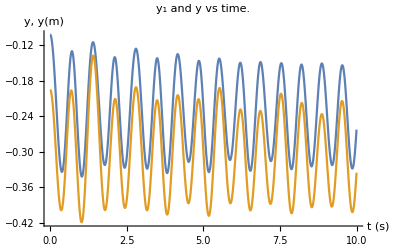

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solnD3],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y(m)"},PlotLabel->"y_1 and y vs time."]
```

Plotting the free support, cylinder and tracking point trajectories in x, y plane.

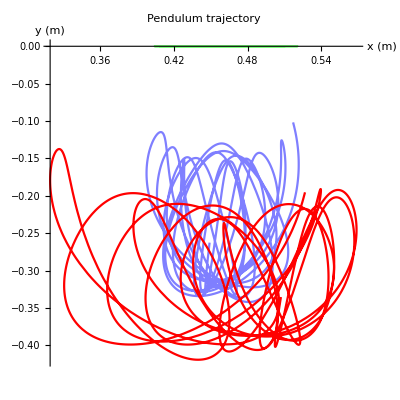

```mathematica
ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solnD3,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle -> {{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red}], AspectRatio->1]
```

Animation of trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[Evaluate[{{Subscript[x, 0],Subscript[y, 0]},{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solnD3,{t,0,tend},PlotRange->{{-0.05,0.15},{-4,0}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory", PlotStyle -> {{Opacity[0.5],Green}, {Opacity[0.5],Blue}, Red}],AspectRatio->1],{tend,0,10},AnimationRepetitions->3,AnimationRate->0.75]
```

```mathematica
Clear["Global`*"]
```

## References

Although the Wilberforce Pendulum is primary used nowadays for physics demonstrations, there is a substantial collection of literary papers outlining and experimenting with the original device. Perhaps the most important piece of reference material for this simulation was an experiment on Wilberforce pendulum oscillations and normal modes by Richard Berg and Todd Marshall (1991), which was used for the simulation values of , , and   . 

1. Berg, R.E. and Marshall, T.S. (1991). Wilberforce pendulum oscillations and normal modes. American Journal of Physics, 59(1), pp.32–38. doi:10.1119/1.16702.

Also see below for an extended list of the papers and resources used:

1. Geballe, R. (1958). Statics and Dynamics of a Helical Spring. American Journal of Physics, 26(5), pp.287–290. doi:10.1119/1.1996131.

2. Hübner, M. and Kröger, J. (2018). Experimental verification of the adiabatic transfer in Wilberforce pendulum normal modes. American Journal of Physics, 86(11), pp.818–824. doi:10.1119/1.5051179.

3. Köpf, U. (1990). Wilberforce’s pendulum revisited. American Journal of Physics, 58(9), pp.833–837. doi:10.1119/1.16376.

4. The Wilberforce Pendulum - Wolfram Demonstrations Project 2018, Wolfram.com, viewed 7 September 2022, <https://demonstrations.wolfram.com/TheWilberforcePendulum/>.

5. Mewes, M. (2014). The Slinky Wilberforce pendulum: A simple coupled oscillator. American Journal of Physics, 82(3), pp.254–256. doi:10.1119/1.4832196.

6. Wilberforce, L.R. (1894). XLIV. On the vibrations of a loaded spiral spring. The London, Edinburgh, and Dublin Philosophical Magazine and Journal of Science, 38(233), pp.386–392. doi:10.1080/14786449408620648.